```mathematica
$Assumptions={X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈
Reals}
```

{X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,Null,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈Reals}

```mathematica
cXStart=-100;
cXStep=0.1;
cXLength= 2000;
cTStep="1.0e-4";
cTStepint = 0.00001;
cTLength="1000000";
cTLengthint=1000000;
cep=0.98;
ccuts=10;
csigma=1;
cdslit=3.0;
```

```mathematica
ϵ=1.0
```

```mathematica
Rf[x_,t_,d_,σ_,a_]:=(σ ((ⅇ^(-((d-x)^2 σ^2)/(4 (a^2 t^2+σ^4)))+ⅇ^(-((d+x)^2 σ^2)/(4 (a^2 t^2+σ^4))))^2-4 ⅇ^(-((d^2+x^2) σ^2)/(2 (a^2 t^2+σ^4))) Sin[(a d t x)/(2 (a^2 t^2+σ^4))]^2))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(a^2 t^2+σ^4))
```

```mathematica
FileLists=0;
FileLists=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-10.dat",Number,RecordLists->True];
FileLists2=0;
FileLists2=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-98.dat",Number,RecordLists->True];
FileLists3=0;
FileLists3=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-95.dat",Number,RecordLists->True];
FileLists4=0;
FileLists4=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-8.dat",Number,RecordLists->True];
FileLists5=0;
FileLists5=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-4.dat",Number,RecordLists->True];
FileLists6=0;
FileLists6=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-0.dat",Number,RecordLists->True];
```

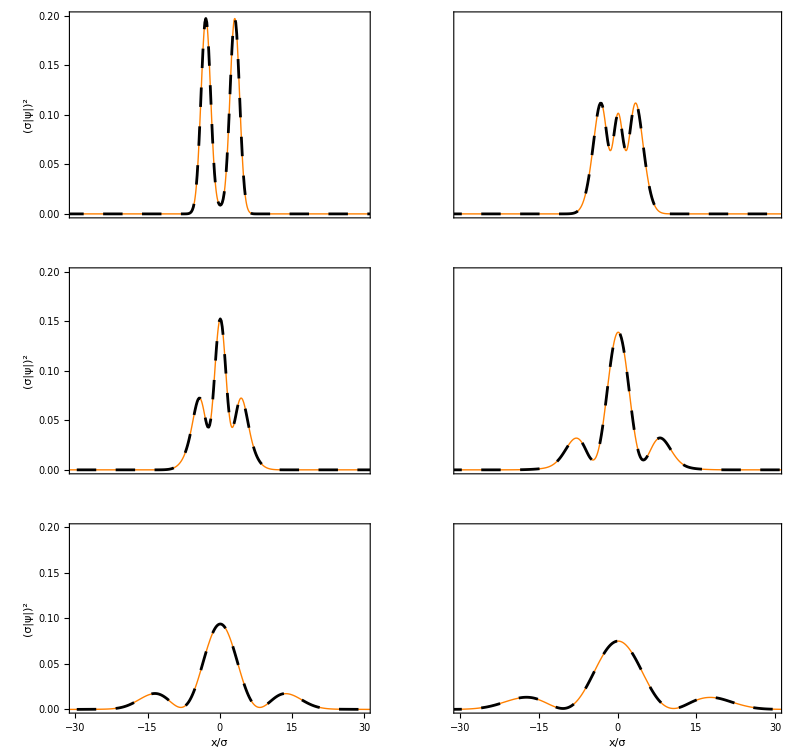

```mathematica
GraphicsGrid[{{Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-1.0)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"σ|ψ|"^2}, RotateLabel->False,FrameTicks->{False,True, False, False}],ListLinePlot[FileLists⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18],ImagePadding->True],Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.98)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False, RotateLabel->False,FrameTicks->{False,False, True, True}],ListLinePlot[FileLists2⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18],ImagePadding->{{22,22},{22,22}}]},{Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.95)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"σ|ψ|"^2}, RotateLabel->False,FrameTicks->{False,True, False, False}],ListLinePlot[FileLists3⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18],ImagePadding->True],Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.8)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False, RotateLabel->False,FrameTicks->{False,False, False, True}],ListLinePlot[FileLists4⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18],ImagePadding->{{22,22},{22,22}}]},{Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.4)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ","σ|ψ|"^2}, RotateLabel->False,FrameTicks->{True,True, False, False}],ListLinePlot[FileLists5⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18],ImagePadding->True],Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.0)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ",""}, RotateLabel->False,FrameTicks->{True,False, False, True}],ListLinePlot[FileLists6⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18],ImagePadding->True]}}]
```

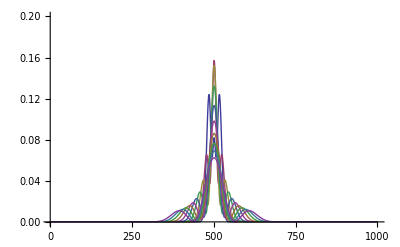

```mathematica
ListLinePlot[FileLists,PlotRange->{Full,{0,0.2}}]
```

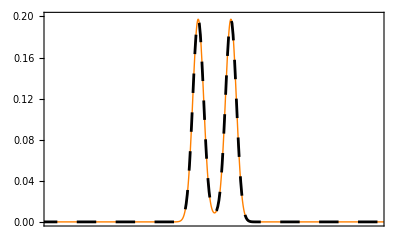

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-1.0)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False, RotateLabel->False,FrameTicks->{False,True, False, False}],ListLinePlot[FileLists⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

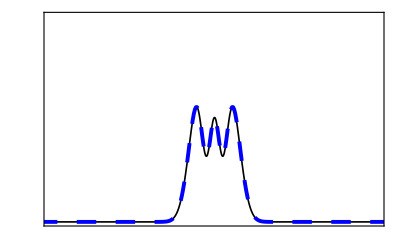

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.98)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Thickness[.003]},Frame->True,Axes->False, RotateLabel->False,FrameTicks->{False,False, True, True}],ListLinePlot[FileLists2⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Blue,Dashing[Large],Thickness[.007]}],LabelStyle->Directive[FontSize->18]]
```

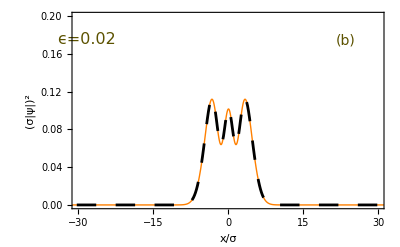

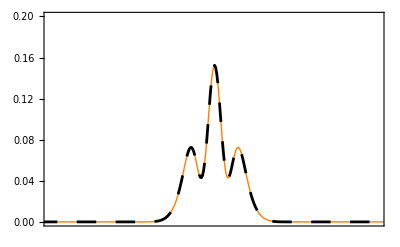

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.95)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False, RotateLabel->False,FrameTicks->{False,True, False, False}],ListLinePlot[FileLists3⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

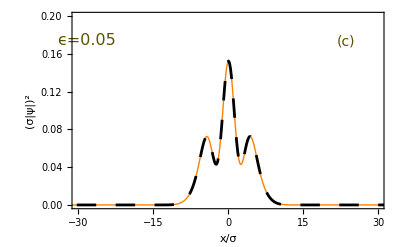

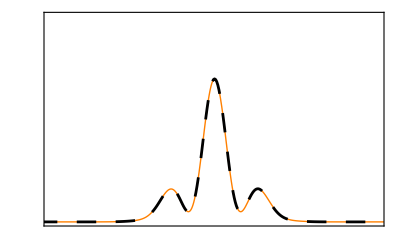

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.8)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False, RotateLabel->False,FrameTicks->{False,False, False, True}],ListLinePlot[FileLists4⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

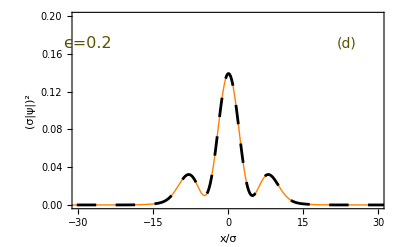

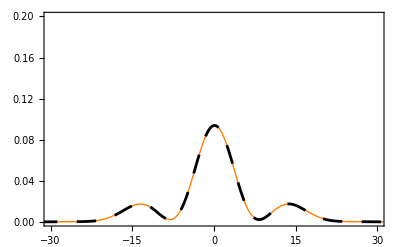

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.4)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False, RotateLabel->False,FrameTicks->{True,True, False, False}],ListLinePlot[FileLists5⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

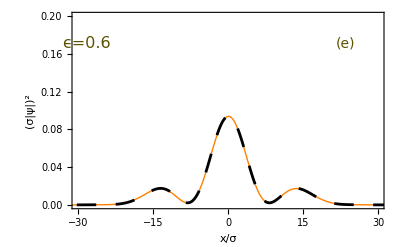

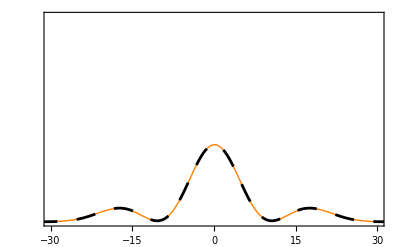

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.0)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False, RotateLabel->False,FrameTicks->{True,False, False, True}],ListLinePlot[FileLists6⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

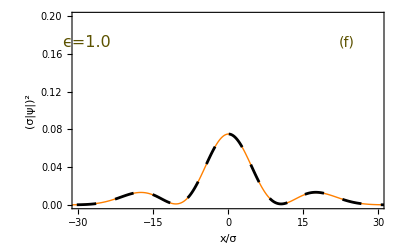

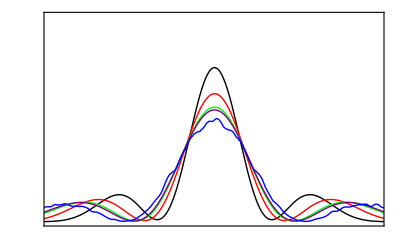

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-cep)1.0],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Black,Frame->True,Axes->False,FrameTicks->None],ListLinePlot[FileLists⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Red,Frame->True,Axes->False],ListLinePlot[FileLists2⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Green,Frame->True,Axes->False],ListLinePlot[FileLists3⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Purple,Frame->True,Axes->False],ListLinePlot[FileLists4⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Blue,Frame->True,Axes->False]]
```